## Critically Damped Lowpass Phase Plot

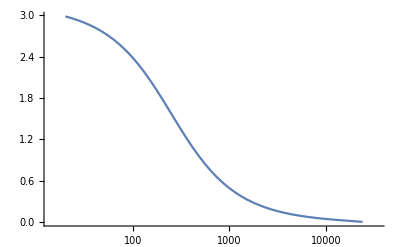

```mathematica
biquadTF[z_,b0_,b1_,b2_,a1_,a2_]:=(b0 z^2 +b1 z + b2)/(-1z^2 -a1 z - a2)

lowpassTF[z_,fc_,sr_,Q_]:=Module[{a0,a1, a2,b0, b1, b2,γ},
γ = Tan[π * fc / sr];

a0= Q*γ^2 + γ + Q;
b0= (Q * γ^2)/a0;
b1= 2 b0;
b2 = b0;
a1 = 2 Q(γ^2-1)/a0;
a2 = (Q γ^2-γ+Q)/a0;

biquadTF[z,b0,b1,b2,a1,a2]
]

z[ω_,sr_]:=ⅇ^(2π ⅈ ω / sr)

LogLinearPlot[Arg[lowpassTF[z[ω,48000],250,48000,0.5]],{ω,20,24000},PlotRange->All]
```

## Second Order Allpass Phase Plot

```mathematica
biquadTF[z_,b0_,b1_,b2_,a1_,a2_]:=(b0 z^2 +b1 z + b2)/(-1z^2 -a1 z - a2)

allpassTF[z_,β_,γ_]:=Module[{a0,a1, a2,b0, b1, b2 (*, γ *)},
(*γ = Tan[π * fc / sr];*)


b0= β;
b1= γ(1+β);
b2 = 1;
a1 = γ(1+β);
a2 = β;

biquadTF[z,b0,b1,b2,a1,a2]
]

z[ω_,sr_]:=ⅇ^(2π ⅈ ω / sr)

Manipulate[
LogLinearPlot[Arg[allpassTF[z[ω,48000],β,-Cos[π 2 ωc/48000]]],{ω,20,24000},PlotRange->π{-1,1}],
{{β,0.5},-1,1},{{ωc,250},20,24000}
]
```

## First Order Allpass Phase Plot

```mathematica
biquadTF[z_,b0_,b1_,b2_,a1_,a2_]:=(b0 z^2 +b1 z + b2)/(-1z^2 -a1 z - a2)

allpass1TF[z_,β_]:=Module[{a0,a1, a2,b0, b1, b2 (*, γ *)},
(*γ = Tan[π * fc / sr];*)


b0= β;
b1= 1;
b2 = 0;
a1 = β;
a2 = 0;

biquadTF[z,b0,b1,b2,a1,a2]
]

z[ω_,sr_]:=ⅇ^(2π ⅈ ω / sr)

Manipulate[
LogLinearPlot[{Arg[allpass1TF[z[ω,48000],Sin[π ( 1ωc/48000)]-Cos[π (1ωc/48000)]]],Arg[lowpassTF[z[ω,48000],ωc,48000,0.5]]},{ω,20,24000},PlotRange->π{0,1}],
{{ωc,12000},20,24000}
]
```

```mathematica
Solve[allpass1TF[z,β]==z ⅇ^(ⅈ π /2),β]//FullSimplify
β[z_]:=-((1-ⅈ)+(1+ⅈ) z^2)/(2 z)
β[z[ω,sr]]//FullSimplify
```

{{β→-((1-ⅈ)+(1+ⅈ) z^2)/(2 z)}}

-Cos[(2 π ω)/sr]+Sin[(2 π ω)/sr]